```mathematica
(* SIR (Cowpox) PREVALENCE *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Cases[Solve[system//.provpars//.pars,{pm,pf,nm,nf,am,af,n}],x_/;x[[1,2]]>0&&x[[2,2]]>0],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Map[Flatten,Table[(Re[pm/.data[[i]][[j]][[2]]])-(Re[pm/.data[[i]][[j]][[1]]]),{i,1,6},{j,1,6}]]/.pm->0
]

(* Provisioning response calculations *)
provpars={δ1p->δ1min+(δ1max-δ1min)*E^(-θ1*prov),α1p->α1max-(α1max-α1min)*E^(-θ2*prov),
δ2p->δ2min+(δ2max-δ2min)*E^(-θ1*prov),α2p->α2max-(α2max-α2min)*E^(-θ2*prov),
δ3p->δ3min+(δ3max-δ3min)*E^(-θ1*prov),α3p->α3max-(α3max-α3min)*E^(-θ2*prov),δ4p->δ4min+(δ4max-δ4min)*E^(-θ1*prov),α4p->α4max-(α4max-α4min)*E^(-θ2*prov)};

(* System equations *)
system={(1-pm)*(δ1p*α1p*am+δ2p*α2p*af)-pm*n/(nm*2)*b*(K-n)/K==0 && 
	   (1-pf)*(δ3p*α3p*am+δ4p*α4p*af)-pf*n/(nf*2)*b*(K-n)/K==0 &&
δ1p*α1p*nm*(1-pm)*am+δ2p*α2p*nm*(1-pm)*af-(ϵ+μ)*am+η*(pm*nm-am)==0&&δ3p*α3p*nf*(1-pf)*am+δ4p*α4p*nf*(1-pf)*af-(ϵ+μ)*af+η*(pf*nf-af)==0&&
b*n/2*(K-n)/K-μ*nm==0 &&
b*n/2*(K-n)/K-μ*nf==0 &&
nm+nf==n };
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars2={K->42.12*1.5,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars3={K->42.12*2,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.359194,0.423206,0.442412,0.449004,0.45137},{-0.203033,0.101863,0.206989,0.238443,0.249227,0.253095},{-0.203033,-0.0798948,0.0545006,0.0947025,0.108484,0.113427},{-0.203033,-0.170665,-0.021673,0.0229034,0.0381843,0.0436653},{-0.203033,-0.203033,-0.0534555,-0.00705504,0.00885144,0.0145568},{-0.203033,-0.203033,-0.0657283,-0.0186239,-0.0024759,0.00331615}}

{{0.,0.212087,0.250435,0.261998,0.265974,0.267401},{-0.287502,0.0598301,0.121768,0.140356,0.146737,0.149027},{-0.490626,-0.0468628,0.0319955,0.05562,0.0637241,0.0666317},{-0.515558,-0.100083,-0.0127161,0.0134422,0.0224135,0.0256319},{-0.515558,-0.122284,-0.0313582,-0.00413975,0.00519442,0.00854297},{-0.515558,-0.130856,-0.0385556,-0.0109273,-0.00145285,0.00194599}}

{{0.,0.147531,0.174566,0.182749,0.185565,0.186577},{-0.19741,0.0413601,0.0843627,0.0973136,0.101765,0.103363},{-0.33646,-0.0323008,0.0220992,0.0384445,0.0440576,0.0460722},{-0.405911,-0.0689052,-0.00877208,0.0092795,0.0154766,0.0177006},{-0.43489,-0.0841547,-0.021622,-0.00285641,0.00358502,0.00589663},{-0.446081,-0.0900405,-0.0265801,-0.00753844,-0.00100253,0.00134294}}

-0.6

0.5

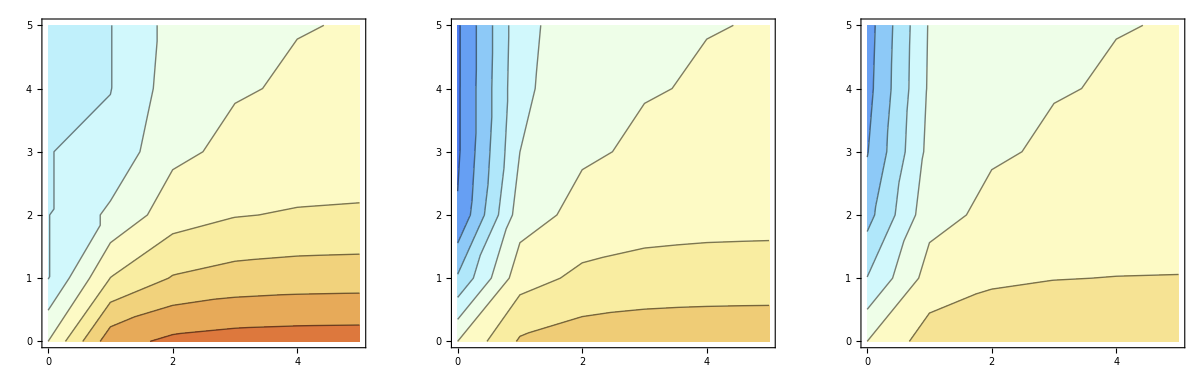

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars2={K->42.12,b->1.24*1.5,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars3={K->42.12,b->1.24*2,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.359194,0.423206,0.442412,0.449004,0.45137},{-0.203033,0.101863,0.206989,0.238443,0.249227,0.253095},{-0.203033,-0.0798948,0.0545006,0.0947025,0.108484,0.113427},{-0.203033,-0.170665,-0.021673,0.0229034,0.0381843,0.0436653},{-0.203033,-0.203033,-0.0534555,-0.00705504,0.00885144,0.0145568},{-0.203033,-0.203033,-0.0657283,-0.0186239,-0.0024759,0.00331615}}

{{0.,0.34963,0.411969,0.430677,0.437099,0.439404},{-0.223208,0.0991386,0.201458,0.232074,0.242571,0.246336},{-0.223208,-0.0777608,0.0530433,0.09217,0.105583,0.110393},{-0.223208,-0.166112,-0.0210938,0.0222911,0.0371634,0.0424978},{-0.223208,-0.202967,-0.0520272,-0.00686646,0.00861481,0.0141677},{-0.223208,-0.217196,-0.0639724,-0.0181261,-0.00240971,0.0032275}}

{{0.,0.345017,0.406549,0.425018,0.431357,0.433632},{-0.232943,0.0978242,0.198789,0.229001,0.23936,0.243076},{-0.232943,-0.0767307,0.05234,0.090948,0.104183,0.10893},{-0.232943,-0.163914,-0.0208142,0.0219956,0.0366707,0.0419343},{-0.232943,-0.200283,-0.0513378,-0.00677544,0.00850061,0.0139799},{-0.232943,-0.214325,-0.0631248,-0.0178859,-0.00237777,0.00318472}}

-0.3

0.5

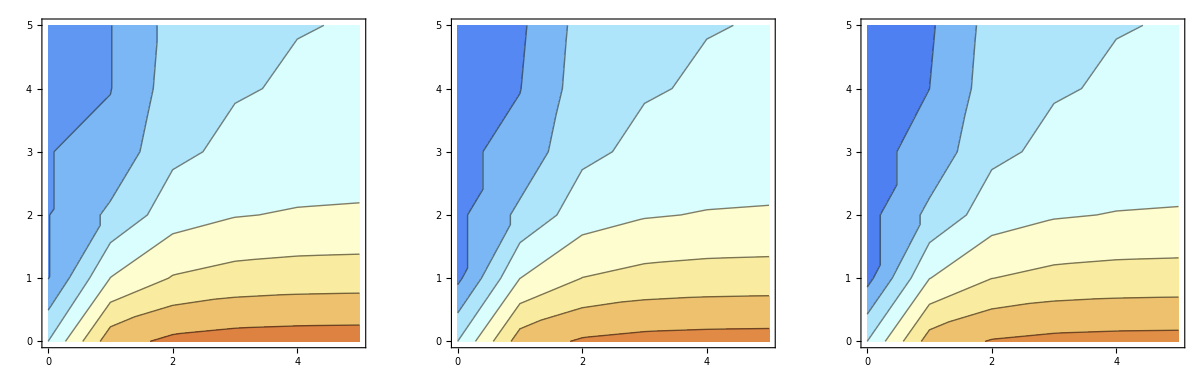

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars2={K->42.12,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75/1.5,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};
pars3={K->42.12,b->1.24,ϵ->0.815,η->0.0132,β1->0.0255,β2->0.0424,β3->0.0148,β4->0.0156,μ->1/13.75/2,δ1max->1*^-1,δ1min->δ1max/2,α1min->β1/δ1max,α1max->α1min*2,
δ2max->1*^-1,δ2min->δ2max/2,α2min->β2/δ2max,α2max->α2min*2,
δ3max->1*^-1,δ3min->δ3max/2,α3min->β3/δ3max,α3max->α3min*2,
δ4max->1*^-1,δ4min->δ4max/2,α4min->β4/δ4max,α4max->α4min*2};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.359194,0.423206,0.442412,0.449004,0.45137},{-0.203033,0.101863,0.206989,0.238443,0.249227,0.253095},{-0.203033,-0.0798948,0.0545006,0.0947025,0.108484,0.113427},{-0.203033,-0.170665,-0.021673,0.0229034,0.0381843,0.0436653},{-0.203033,-0.203033,-0.0534555,-0.00705504,0.00885144,0.0145568},{-0.203033,-0.203033,-0.0657283,-0.0186239,-0.0024759,0.00331615}}

{{0.,0.30619,0.360944,0.377395,0.383044,0.385072},{-0.315005,0.0867485,0.176314,0.203128,0.212323,0.215622},{-0.315005,-0.0680416,0.0464123,0.0806502,0.0923878,0.096598},{-0.315005,-0.145365,-0.0184567,0.0195043,0.0325174,0.0371849},{-0.315005,-0.177627,-0.0455236,-0.00600802,0.00753779,0.0123964},{-0.315005,-0.190085,-0.055976,-0.01586,-0.00210845,0.002824}}

{{0.,0.271253,0.319917,0.334554,0.339582,0.341388},{-0.369547,0.0767642,0.156072,0.17983,0.18798,0.190904},{-0.389117,-0.0601955,0.0410665,0.0713666,0.0817557,0.0854824},{-0.389117,-0.1286,-0.0163291,0.0172569,0.0287712,0.0329013},{-0.389117,-0.157143,-0.0402748,-0.00531553,0.00666911,0.0109679},{-0.389117,-0.168165,-0.0495216,-0.0140318,-0.00186544,0.00249853}}

-0.4

0.5

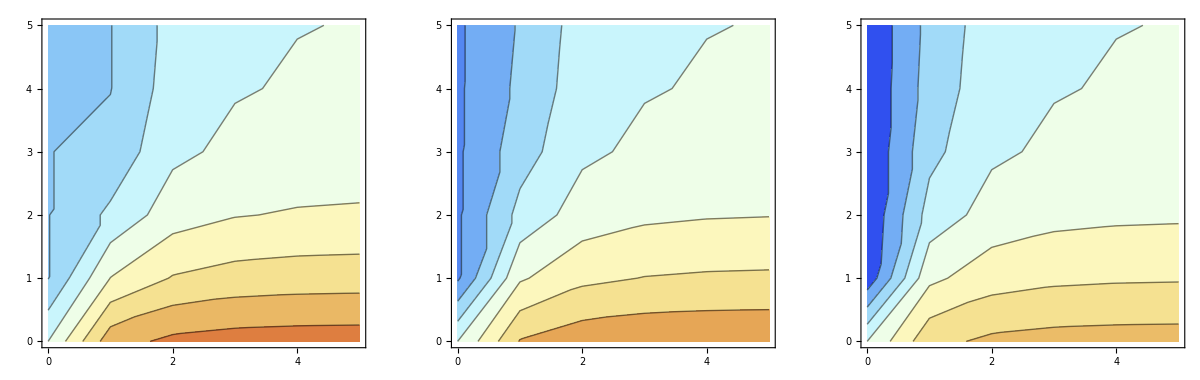

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```